## Differences between primes

```mathematica
Get[StringJoin[NotebookDirectory[] , "nprimes.mx"]]
```

```mathematica
results={};
n=12;
primes=nprimes[[n,;;50000]];
```

## Prime 12

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
series=Table[{x,diffs[[x]]},{x,Length@diffs}];
(* Removed first, 2 -> 3, the only transition with d = 1 *)
```

## Visibility Graph

```mathematica
natLinks =naturalVisibility[series];
```

## Graph

```mathematica
igv11=Graph[natLinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv11];
```

```mathematica
count = Total[adj]//Counts
```

<|3→9098,4→8485,8→2349,10→1390,39→18,2→6305,6→4486,9→1781,28→72,5→6408,7→3231,12→878,17→320,13→662,14→597,11→1096,19→214,44→11,15→460,25→100,20→194,23→144,30→48,46→10,57→3,72→2,132→1,32→31,31→45,18→267,26→79,16→349,21→166,22→138,45→14,40→7,67→2,24→97,42→19,27→78,35→27,36→27,33→44,29→46,69→2,51→7,38→28,37→32,54→3,63→1,76→1,80→1,81→1,85→2,56→6,95→1,146→1,73→1,59→4,66→2,64→2,89→1,68→1,102→1,48→7,34→29,58→2,43→10,50→6,47→9,41→9,53→2,61→4,55→4,52→4,60→4,71→1,70→2,65→2,49→1,75→2,97→1,86→1,91→1,1→1|>

```mathematica
count=count[[2;;]]
```

<|180→2,181→4,182→9,184→1,172→1,162→1,160→2,289→1,111→8,117→14,114→7,120→7,115→8,123→4,112→11,107→6,294→1,96→11,100→12,110→7,94→11,106→5,109→6,113→9,116→3,118→7,325→2,98→7,95→11,105→9,103→8,92→6,259→1,102→8,350→1,99→7,97→9,108→12,104→6,93→5,101→5,127→5,384→1,79→14,64→14,84→14,71→25,82→14,54→42,67→26,57→33,56→36,53→53,698→1,47→70,59→29,38→158,943→1,58→36,39→131,66→20,55→38,76→22,69→16,63→18,41→110,78→7,868→1,34→131,50→60,46→65,51→60,36→171,1389→1,75→23,33→124,35→150,37→175,44→90,45→60,1728→1,1634→1,40→131,30→89,8→287,5→627,25→33,12→164,11→195,31→87,6→500,26→45,20→94,16→105,3→1024,4→745,10→246,19→70,23→66,21→82,15→107,14→110,17→91,2→597,2293→1,48→69,22→69,18→96,13→117,9→249,7→369,24→48,29→71,28→82,164→1,187→1,183→4,179→1,190→2,177→1,186→1,188→1,195→1,175→1,171→1,255→3,231→2,169→1,81→19,453→1,193→1,90→16,88→2,91→12,280→1,62→25,254→2,89→9,77→11,455→1,83→12,60→22,52→49,85→9,86→15,119→6,87→8,74→22,121→2,359→2,625→1,602→1,65→23,32→85,200→1,207→1,209→1,140→3,72→19,70→22,122→5,73→17,42→94,68→20,221→1,138→4,61→20,735→1,1766→1,135→2,139→3,49→59,658→1,134→4,131→2,409→1,498→1,366→1,487→1,508→1,533→1,407→1,480→1,422→1,512→1,559→1,490→1,563→1,303→1,143→3,146→1,465→1,592→1,348→1,206→1,320→1,201→1,212→2,214→1,942→1,643→1,220→1,232→1,448→1,328→1,125→2,851→1,1400→1,803→1,154→3,241→1,43→82,155→2,129→4,784→1,266→1,80→17,599→1,128→4,130→3,397→1,751→1,152→1,1130→1,203→1,793→2,1343→1,665→1,238→1,543→1,415→1,669→1,202→1,996→1,204→1,1015→1,824→2,389→1,249→1,940→1,132→1,133→1,855→1,1553→1,151→2,347→1,198→1,774→1,1068→1,649→1,240→1,351→1,383→1,136→1,491→1,659→1,230→2,1612→1,235→1,1157→1,147→2,194→1,159→1,148→1,1477→1,1348→1,145→3,124→2,156→1,229→1,126→1,1920→1,1203→1,27→53,1670→1,1153→1,1223→1,1336→1,153→3,1542→1,375→1,191→1,349→1,144→1,1083→1,520→1,142→1,982→1,1485→1,948→1,199→2,2307→1,1429→1,1494→1,944→1,1740→1,1806→1,1148→1,936→1,1921→1,150→1,1759→2,2348→1,1973→1,2125→1,2410→1,2343→1,2070→1,1885→1,2474→1,2347→1,211→1,137→2,700→1,2175→1,1387→1,2315→1,1720→1,1915→1,1587→1,2094→1,958→1,1819→1,2266→1,1258→1,1708→2,1648→2,2145→1,1599→1,1419→1,1651→1,1799→1,1772→1,1659→1,766→1,1894→1,1770→1,1661→1,1471→1,1562→1,1705→1,1726→1,224→1,1567→1,189→1,1908→1,1180→1,1686→1,2144→1,2451→1,1660→1,1675→1,1919→1,1787→1,1752→1,1559→1,1848→1,1711→1,1769→1,1546→1,1667→1,1665→1,1853→1,1715→1,1589→1,1603→1,1706→1|>

```mathematica
count[1]=.
```

```mathematica
count=Sort[count]
```

<|132→1,63→1,76→1,80→1,81→1,95→1,146→1,73→1,89→1,68→1,102→1,71→1,49→1,97→1,86→1,91→1,1→1,72→2,67→2,69→2,85→2,66→2,64→2,58→2,53→2,70→2,65→2,75→2,57→3,54→3,59→4,61→4,55→4,52→4,60→4,56→6,50→6,40→7,51→7,48→7,47→9,41→9,46→10,43→10,44→11,45→14,39→18,42→19,35→27,36→27,38→28,34→29,32→31,37→32,33→44,31→45,29→46,30→48,28→72,27→78,26→79,24→97,25→100,22→138,23→144,21→166,20→194,19→214,18→267,17→320,16→349,15→460,14→597,13→662,12→878,11→1096,10→1390,9→1781,8→2349,7→3231,6→4486,2→6305,5→6408,4→8485,3→9098|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{132,1/49999},{63,1/49999},{76,1/49999},{80,1/49999},{81,1/49999},{95,1/49999},{146,1/49999},{73,1/49999},{89,1/49999},{68,1/49999},{102,1/49999},{71,1/49999},{49,1/49999},{97,1/49999},{86,1/49999},{91,1/49999},{72,2/49999},{67,2/49999},{69,2/49999},{85,2/49999},{66,2/49999},{64,2/49999},{58,2/49999},{53,2/49999},{70,2/49999},{65,2/49999},{75,2/49999},{57,3/49999},{54,3/49999},{59,4/49999},{61,4/49999},{55,4/49999},{52,4/49999},{60,4/49999},{56,6/49999},{50,6/49999},{40,7/49999},{51,7/49999},{48,7/49999},{47,9/49999},{41,9/49999},{46,10/49999},{43,10/49999},{44,11/49999},{45,14/49999},{39,18/49999},{42,19/49999},{35,27/49999},{36,27/49999},{38,28/49999},{34,29/49999},{32,31/49999},{37,32/49999},{33,44/49999},{31,45/49999},{29,46/49999},{30,48/49999},{28,72/49999},{27,78/49999},{26,79/49999},{24,97/49999},{25,100/49999},{22,138/49999},{23,144/49999},{21,166/49999},{20,194/49999},{19,214/49999},{18,267/49999},{17,320/49999},{16,349/49999},{15,460/49999},{14,597/49999},{13,662/49999},{12,878/49999},{11,1096/49999},{10,1390/49999},{9,1781/49999},{8,2349/49999},{7,3231/49999},{6,4486/49999},{2,6305/49999},{5,6408/49999},{4,8485/49999},{3,9098/49999}}

```mathematica
countrel = countrel[[2;;]]
```

{{181,4/9999},{182,1/1111},{184,1/9999},{172,1/9999},{162,1/9999},{160,2/9999},{289,1/9999},{111,8/9999},{117,14/9999},{114,7/9999},{120,7/9999},{115,8/9999},{123,4/9999},{112,1/909},{107,2/3333},{294,1/9999},{96,1/909},{100,4/3333},{110,7/9999},{94,1/909},{106,5/9999},{109,2/3333},{113,1/1111},{116,1/3333},{118,7/9999},{325,2/9999},{98,7/9999},{95,1/909},{105,1/1111},{103,8/9999},{92,2/3333},{259,1/9999},{102,8/9999},{350,1/9999},{99,7/9999},{97,1/1111},{108,4/3333},{104,2/3333},{93,5/9999},{101,5/9999},{127,5/9999},{384,1/9999},{79,14/9999},{64,14/9999},{84,14/9999},{71,25/9999},{82,14/9999},{54,14/3333},{67,26/9999},{57,1/303},{56,4/1111},{53,53/9999},{698,1/9999},{47,70/9999},{59,29/9999},{38,158/9999},{943,1/9999},{58,4/1111},{39,131/9999},{66,20/9999},{55,38/9999},{76,2/909},{69,16/9999},{63,2/1111},{41,10/909},{78,7/9999},{868,1/9999},{34,131/9999},{50,20/3333},{46,65/9999},{51,20/3333},{36,19/1111},{1389,1/9999},{75,23/9999},{33,124/9999},{35,50/3333},{37,175/9999},{44,10/1111},{45,20/3333},{1728,1/9999},{1634,1/9999},{40,131/9999},{30,89/9999},{8,287/9999},{5,19/303},{25,1/303},{12,164/9999},{11,65/3333},{31,29/3333},{6,500/9999},{26,5/1111},{20,94/9999},{16,35/3333},{3,1024/9999},{4,745/9999},{10,82/3333},{19,70/9999},{23,2/303},{21,82/9999},{15,107/9999},{14,10/909},{17,91/9999},{2,199/3333},{2293,1/9999},{48,23/3333},{22,23/3333},{18,32/3333},{13,13/1111},{9,83/3333},{7,41/1111},{24,16/3333},{29,71/9999},{28,82/9999},{164,1/9999},{187,1/9999},{183,4/9999},{179,1/9999},{190,2/9999},{177,1/9999},{186,1/9999},{188,1/9999},{195,1/9999},{175,1/9999},{171,1/9999},{255,1/3333},{231,2/9999},{169,1/9999},{81,19/9999},{453,1/9999},{193,1/9999},{90,16/9999},{88,2/9999},{91,4/3333},{280,1/9999},{62,25/9999},{254,2/9999},{89,1/1111},{77,1/909},{455,1/9999},{83,4/3333},{60,2/909},{52,49/9999},{85,1/1111},{86,5/3333},{119,2/3333},{87,8/9999},{74,2/909},{121,2/9999},{359,2/9999},{625,1/9999},{602,1/9999},{65,23/9999},{32,85/9999},{200,1/9999},{207,1/9999},{209,1/9999},{140,1/3333},{72,19/9999},{70,2/909},{122,5/9999},{73,17/9999},{42,94/9999},{68,20/9999},{221,1/9999},{138,4/9999},{61,20/9999},{735,1/9999},{1766,1/9999},{135,2/9999},{139,1/3333},{49,59/9999},{658,1/9999},{134,4/9999},{131,2/9999},{409,1/9999},{498,1/9999},{366,1/9999},{487,1/9999},{508,1/9999},{533,1/9999},{407,1/9999},{480,1/9999},{422,1/9999},{512,1/9999},{559,1/9999},{490,1/9999},{563,1/9999},{303,1/9999},{143,1/3333},{146,1/9999},{465,1/9999},{592,1/9999},{348,1/9999},{206,1/9999},{320,1/9999},{201,1/9999},{212,2/9999},{214,1/9999},{942,1/9999},{643,1/9999},{220,1/9999},{232,1/9999},{448,1/9999},{328,1/9999},{125,2/9999},{851,1/9999},{1400,1/9999},{803,1/9999},{154,1/3333},{241,1/9999},{43,82/9999},{155,2/9999},{129,4/9999},{784,1/9999},{266,1/9999},{80,17/9999},{599,1/9999},{128,4/9999},{130,1/3333},{397,1/9999},{751,1/9999},{152,1/9999},{1130,1/9999},{203,1/9999},{793,2/9999},{1343,1/9999},{665,1/9999},{238,1/9999},{543,1/9999},{415,1/9999},{669,1/9999},{202,1/9999},{996,1/9999},{204,1/9999},{1015,1/9999},{824,2/9999},{389,1/9999},{249,1/9999},{940,1/9999},{132,1/9999},{133,1/9999},{855,1/9999},{1553,1/9999},{151,2/9999},{347,1/9999},{198,1/9999},{774,1/9999},{1068,1/9999},{649,1/9999},{240,1/9999},{351,1/9999},{383,1/9999},{136,1/9999},{491,1/9999},{659,1/9999},{230,2/9999},{1612,1/9999},{235,1/9999},{1157,1/9999},{147,2/9999},{194,1/9999},{159,1/9999},{148,1/9999},{1477,1/9999},{1348,1/9999},{145,1/3333},{124,2/9999},{156,1/9999},{229,1/9999},{126,1/9999},{1920,1/9999},{1203,1/9999},{27,53/9999},{1670,1/9999},{1153,1/9999},{1223,1/9999},{1336,1/9999},{153,1/3333},{1542,1/9999},{375,1/9999},{191,1/9999},{349,1/9999},{144,1/9999},{1083,1/9999},{520,1/9999},{142,1/9999},{982,1/9999},{1485,1/9999},{948,1/9999},{199,2/9999},{2307,1/9999},{1429,1/9999},{1494,1/9999},{944,1/9999},{1740,1/9999},{1806,1/9999},{1148,1/9999},{936,1/9999},{1921,1/9999},{150,1/9999},{1759,2/9999},{2348,1/9999},{1973,1/9999},{2125,1/9999},{2410,1/9999},{2343,1/9999},{2070,1/9999},{1885,1/9999},{2474,1/9999},{2347,1/9999},{211,1/9999},{137,2/9999},{700,1/9999},{2175,1/9999},{1387,1/9999},{2315,1/9999},{1720,1/9999},{1915,1/9999},{1587,1/9999},{2094,1/9999},{958,1/9999},{1819,1/9999},{2266,1/9999},{1258,1/9999},{1708,2/9999},{1648,2/9999},{2145,1/9999},{1599,1/9999},{1419,1/9999},{1651,1/9999},{1799,1/9999},{1772,1/9999},{1659,1/9999},{766,1/9999},{1894,1/9999},{1770,1/9999},{1661,1/9999},{1471,1/9999},{1562,1/9999},{1705,1/9999},{1726,1/9999},{224,1/9999},{1567,1/9999},{189,1/9999},{1908,1/9999},{1180,1/9999},{1686,1/9999},{2144,1/9999},{2451,1/9999},{1660,1/9999},{1675,1/9999},{1919,1/9999},{1787,1/9999},{1752,1/9999},{1559,1/9999},{1848,1/9999},{1711,1/9999},{1769,1/9999},{1546,1/9999},{1667,1/9999},{1665,1/9999},{1853,1/9999},{1715,1/9999},{1589,1/9999},{1603,1/9999},{1706,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.427002/x^1.09597]

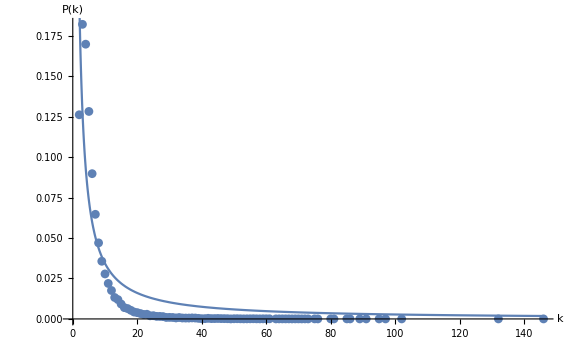

```mathematica
vis11=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-11.eps",vis11];
```

## Mean degree

```mathematica
degree=VertexDegree[igv11]//Mean//N
```

6.34505

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horLinks=horizontalVisibility[series];
```

## Graph

```mathematica
igh11=Graph[horLinks, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh11];
```

```mathematica
count = Total[adj]//Counts
```

<|2→18988,3→10882,7→2054,13→133,4→7079,8→1219,6→2940,10→512,16→43,9→738,11→338,5→4645,15→59,20→10,18→14,14→87,12→219,21→4,17→20,19→12,22→1,24→1,1→1|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{2,18988/49999},{3,10882/49999},{7,2054/49999},{13,133/49999},{4,7079/49999},{8,1219/49999},{6,2940/49999},{10,512/49999},{16,43/49999},{9,738/49999},{11,338/49999},{5,4645/49999},{15,59/49999},{20,10/49999},{18,14/49999},{14,87/49999},{12,219/49999},{21,4/49999},{17,20/49999},{19,12/49999},{22,1/49999},{24,1/49999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.31549/x^1.73943]

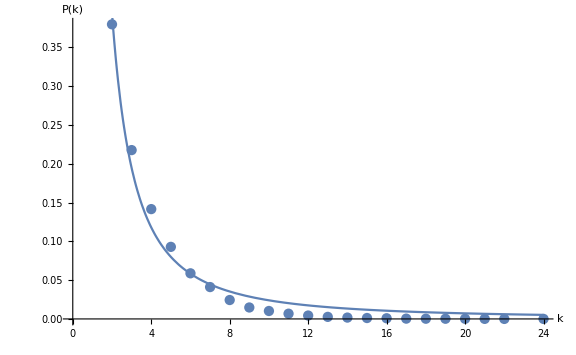

```mathematica
hvis11=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-11.eps",hvis11];
```

## Mean degree

```mathematica
degree=VertexDegree[igh11]//Mean//N
```

3.75432

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
results
```

{{visibility,12,49999,6.34505,1.09597 ± 0.150575,0.427002 ± 0.0938365},{horizontal,12,49999,3.75432,1.73943 ± 0.154409,1.31549 ± 0.195506}}